12

2 √21

1/4 (1+x) √(-1-2 x+3 x^2)

-1/16+x/4-x^2/8-x^3/4+(3 x^4)/16

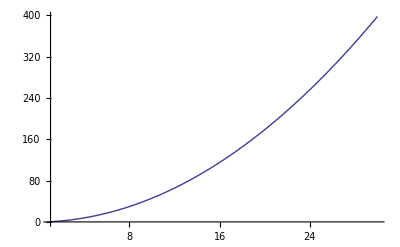

2 (1+2 n) √(n (1+3 n))

```mathematica
Clear[x]

AreaAlmostEqTri[x_,delta_]:=(x+delta)/2 Sqrt[x^2-((x+delta)/2)^2]
AreaAlmostEqTri[5,+1]
AreaAlmostEqTri[5,-1]
Simplify[AreaAlmostEqTri[x,+1]]
Expand[AreaAlmostEqTri[x,-1]^2]

(*
Solve[AreaAlmostEqTri[x,+1]==12&&x>0&&x∈Integers]
*)

Plot[AreaAlmostEqTri[x,+1],{x,1,30}]

Simplify[AreaAlmostEqTri[4n+1,+1]]
```

```mathematica
xs=Map[{#,AreaAlmostEqTri[#,+1]}&,Range[2,1000000]];
ys=Select[xs,IntegerQ[#[[2]]]&]
Total[Map[3#[[1]]+1&,ys]]
```

{{5,12},{65,1848},{901,351780},{12545,68149872},{174725,13219419708}}

564728

```mathematica
target=1000

(*
Map[AreaAlmostEqTri[#,+1]&,Range[2,Ceiling[Sqrt[target]]]]
*)
```

10000

```mathematica
Total[{16,196,2704,37636,50,722,10082}]
```

51406

```mathematica
(1000000000-1)/3
```

```mathematica
Sqrt[N[AreaAlmostEqTri[333333333,+1]]]
```

2.19346×10^8

```mathematica
SetAttributes[squareQ,Listable];
squareQ[x_]:=MatchQ[Head[x],Integer|Rational]&&And@@OddQ[DivisorSigma[0,Through[{Numerator,Denominator}[x]]]]
f[x_]:={x,squareQ[-1-2 x+3 x^2]}
xs=Map[f,Range[1,1000000]];
Select[xs,#[[2]]&]
```

{{5,True},{65,True},{901,True},{12545,True},{174725,True}}

```mathematica
ClearAll["Global`*"]
Reduce[1/4 (1+x) √(-1-2 x+3 x^2)==y,x]
```

```mathematica
c^2==a^2+b^2
c^2== 2a^2
Solve[(a+1)^2==2a^2,a]
```

c^2==a^2+b^2

c^2==2 a^2

{{a→1-√2},{a→1+√2}}

```mathematica
(*

Side 1 = x
Side 2 = x
Side 3 = x+1

Area of right triangle
a b /2

Consider half a triangle, split along side 3
Side 1 = x
Side 3 = (x+1)/2
Side 3 = Sqrt[x^2 - ((x+1)/2)^2]

Area of an almost equal
 a b 
sum of two right triangles

(x+1) Sqrt[x^2 - ((x+1)/2)^2]
*)
```

```mathematica
ClearAll["Global`*"]
triarea[a_,b_,c_]:=Module[{s},
s=(a+b+c)/2;
Return[Sqrt[s(s-a)(s-b)(s-c)]]
]

FullSimplify[triarea[x,x,x+1],x>1&&x∈Integers]/.x->2k
```

1/4 (1+2 k) √((-1+2 k) (1+6 k))